# Programación Funcional

C. Guerra
cesarg@wolfram.com

## Expresiones y Funciones

### Expresiones Atómicas

Head[expr]       		The head of expr

#### Símbolos

```mathematica
{Head[f],Head[Integrate]}
```

{Symbol,Symbol}

```mathematica
{Head[π],Head[ⅇ]}
```

{Symbol,Symbol}

#### Enteros y reales

```mathematica
{Head[7],Head[7.0]}
```

{Integer,Real}

```mathematica
Head[N[7/17,30]]
```

Real

#### Cadenas y caracteres

```mathematica
Head["Mathematica"]
```

String

```mathematica
{Head["α"],Head["π"]}
```

{String,String}

#### Racionales y complejos

```mathematica
{Head[7/3],Head[1+3I]}
```

{Rational,Complex}

```mathematica
{Rational[7,3],Complex[1,3]}
```

{7/3,1+3 ⅈ}

```mathematica
ⅈ==Complex[0,1]
```

True

## Expresiones y Funciones

### Expresiones Compuestas

head[expr1, expr2,…]	Forma interna de una expresión compuesta
FullForm[expr]   		Mostrar la forma interna de una expresión

#### Ejemplos

```mathematica
a+b+c//FullForm
```

Plus[a,b,c]

```mathematica
Plus[a,b,c]
```

a+b+c

```mathematica
a+b+c//Head
```

Plus

```mathematica
Integer[7]
```

Integer[7]

```mathematica
a b c//FullForm
```

Times[a,b,c]

```mathematica
{a,b,c}//FullForm
```

List[a,b,c]

#### Ejemplo: Expresion trigonométrica

```mathematica
expr=(x+y)Sin[a x^2+b x ]Tan[a y^2+b y ]
```

(x+y) Sin[b x+a x^2] Tan[b y+a y^2]

```mathematica
expr//FullForm
```

Times[Plus[x,y],Sin[Plus[Times[b,x],Times[a,Power[x,2]]]],Tan[Plus[Times[b,y],Times[a,Power[y,2]]]]]

```mathematica
(x+y) Sin[b x+a x^2] Tan[b y+a y^2]
```

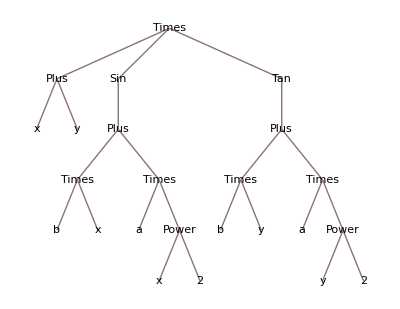

```mathematica
expr//TreeForm
```

```mathematica
Head[expr]
```

Times

## Expresiones y Funciones

### Operaciones sobre una Expresión

#### Partes de una expresión

```mathematica
Part[a+b,1]
```

a

```mathematica
Part[a+b,2]
```

b

```mathematica
a+ⅈ b//FullForm
```

Plus[a,Times[Complex[0,1],b]]

```mathematica
Part[a+ⅈ b,0]
```

Plus

```mathematica
Part[a+ⅈ b,1]
```

a

```mathematica
Part[a+ⅈ b,2]
```

ⅈ b

```mathematica
(a+ⅈ b)[[2,1]]
```

ⅈ

##### Parte de los racionales y complejos

```mathematica
5/7//FullForm
```

Rational[5,7]

```mathematica
Part[5/7,0]
```

Rational

```mathematica
Part[5/7,1]
```

Part::partd: Part specification 5/7⟦1⟧ is longer than depth of object.

5/7⟦1⟧

```mathematica
Part[2+ⅈ,0]
```

Complex

```mathematica
Part[2+ⅈ,1]
```

Part::partd: Part specification (2+ⅈ)⟦1⟧ is longer than depth of object.

(2+ⅈ)⟦1⟧

#### Operaciones heredadas de listas

```mathematica
Length[{a,b,c}]
```

3

```mathematica
Length[Plus[a,b,c]]
```

3

```mathematica
Append[List[a,b,v],d]
```

{a,b,v,d}

```mathematica
Append[f[a,b,c,d],e]
```

f[a,b,c,d,e]

```mathematica
x+w y//FullForm
```

Plus[x,Times[w,y]]

```mathematica
Append[x+w y,z]
```

x+w y+z

```mathematica
RotateLeft[f[a,v,b,f,d]]
```

f[v,b,f,d,a]

## Expresiones y Funciones

### Atributos de un símbolo (función)

Attributes[f]         	  		Give the attributes of f
SetAttributes[f, attr]			Add attr to the attributes of f
ClearAttributes[f, attr]  		Remove attr from the attributes of f
Attributes[f] = {}    	   		Remove all attributes of f

Input         	Output                                                                                          
Listable    	f[{x,y,z}]   	{f[x],f[y],f[z]}		f is applied to each list element
Orderless   	f[y,z,x]     	f[x,y,z]         		Arguments are first sorted
Flat        	f[f[x,y],z]  	f[x,y,z]         		Arguments are “flattened out”
Constant    	D[f,x]       	0                		All derivatives of f are zero
       
HoldAll				No arguments of f are evaluated
HoldFirst
NumericFunction   	f is assumed to be a numeric quantity for numeric arguments
Protected         	Values of f cannot be changed

Los atributos son propiedades asignadas a una función o símbolo de manera que modifican su comportamiento.

#### Flat

##### Ejemplo

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
{((a+b)+c)+d,Plus[Plus[a+b],c]}
```

{a+b+c+d,a+b+c}

##### Ejemplo

```mathematica
plus[plus[a,b],c]
```

plus[plus[a,b],c]

```mathematica
SetAttributes[plus,Flat]
```

```mathematica
plus[plus[plus[a,b],plus[c,d]]]
```

plus[a,b,c,d]

#### Listable

##### Ejemplo

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

```mathematica
Sin[{2,3,4}]
```

{Sin[2],Sin[3],Sin[4]}

```mathematica
Sin[{{2},{3},{4}}]
```

{{Sin[2]},{Sin[3]},{Sin[4]}}

##### Ejemplo

```mathematica
SetAttributes[plus,Listable]
```

```mathematica
plus[{a,b,c}]
```

{plus[a],plus[b],plus[c]}

```mathematica
Clear[x]
```

```mathematica
plus[{a,b,c},x]
```

{plus[a,x],plus[b,x],plus[c,x]}

```mathematica
plus[{a,b,c},{x,y,z}]
```

{plus[a,x],plus[b,y],plus[c,z]}

```mathematica
plus[{a,b,c},{w,x,y,z}]
```

Thread::tdlen: Objects of unequal length in plus[{a,b,c},{w,x,y,z}] cannot be combined.

plus[{a,b,c},{w,x,y,z}]

##### Ejemplo

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
{a,b,c}+{x,y,z}
```

{a+x,b+y,c+z}

```mathematica
Plus[{a,b,c},{x,y,z},{m,n,p}]
```

{a+m+x,b+n+y,c+p+z}

```mathematica
Plus[{{a,a2},{b,b2},{c,c2}},{{x,x2},{y,y2},{z,z2}}]
```

{{a+x,a2+x2},{b+y,b2+y2},{c+z,c2+z2}}

```mathematica
Plus[{a,b,c},{w,x,y,z}]
```

Thread::tdlen: Objects of unequal length in {a,b,c}+{w,x,y,z} cannot be combined.

{a,b,c}+{w,x,y,z}

##### Ejemplo

```mathematica
Attributes[Log]
```

{Listable,NumericFunction,Protected}

```mathematica
Log[{a,s,d,f}]
```

{Log[a],Log[s],Log[d],Log[f]}

```mathematica
Log[2,a]
```

Log[a]/Log[2]

```mathematica
Log[2,{a,b,c}]
```

{Log[a]/Log[2],Log[b]/Log[2],Log[c]/Log[2]}

```mathematica
Log[{2,3,4},x]
```

{Log[x]/Log[2],Log[x]/Log[3],Log[x]/Log[4]}

```mathematica
Log[{2,3,4},{x,y,z}]
```

{Log[x]/Log[2],Log[y]/Log[3],Log[z]/Log[4]}

##### Ejemplo

```mathematica
SetAttributes[abs,Listable]
```

```mathematica
abs[x_]:=If[x≥0,x,-x]
```

```mathematica
abs[{-2,-1,0,1,2}]
```

{2,1,0,1,2}

#### HoldAll, HoldFirst, …

##### Ejemplo

```mathematica
??Set
```

lhs=rhs evaluates rhs and assigns the result to be the value of lhs. From then on, lhs is replaced by rhs whenever it appears. 
{l_1,l_2,…}={r_1,r_2,…} evaluates the r_i, and assigns the results to be the values of the corresponding l_i.

Attributes[Set]={HoldFirst,Protected,SequenceHold}

```mathematica
??SetDelayed
```

lhs:=rhs assigns rhs to be the delayed value of lhs. rhs is maintained in an unevaluated form. When lhs appears, it is replaced by rhs, evaluated afresh each time.

Attributes[SetDelayed]={HoldAll,Protected,SequenceHold}

##### Ejemplo: Table

```mathematica
Attributes[Table]
```

{HoldAll,Protected}

```mathematica
ReplacePart[gg[i,1,10],0->List]
```

{i,1,10}

```mathematica
Table[f[i],{i,1,10}]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
ReplacePart[gg[i,1,10],0->List]
```

{i,1,10}

```mathematica
Table[f[i],Evaluate@ReplacePart[gg[i,1,10],0->List]]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
ReplacePart[Prepend[Tuples[{{p,q,r},{{True,False}}}],p∧q],0->Table]
```

{{{True,True},{False,False}},{{False,False},{False,False}}}

```mathematica
Sequence@@Tuples[{{p,q,r},{{True,False}}}]
```

Sequence[{p,{True,False}},{q,{True,False}},{r,{True,False}}]

```mathematica
Table[{p,q},Sequence@@Tuples[{{p,q},{{True,False}}}]]
```

```mathematica
Table[{p,q},Evaluate@(Sequence@@Tuples[{{p,q},{{True,False}}}])]
```

## Manipulación de Expresiones

### Mapeando una función

Map[f,{a,b,c}]  or  f /@ {a,b,c}   		Calculate {f[a],f[b],f[c]}
Map[f,h[a,b,c]]  or  f /@ h[a,b,c]   	Calculate h[f[a],f[b],f[c]]
Map[f, expr, levels]     				Map f to the specified levels of expr
MapAt[f, expr, parts]    				Map f to the specified parts of expr
MapIndexed[f,expr]						Map with indexes

#### Map

##### Ejemplos básicos

```mathematica
Map[f,{a,{b},c}]
```

{f[a],f[{b}],f[c]}

```mathematica
Map[f,List[a,b,c]]
```

{f[a],f[b],f[c]}

```mathematica
Clear[g]
```

```mathematica
Map[f,g[a,b,c]]
```

g[f[a],f[b],f[c]]

```mathematica
f/@g[a,b,c]
```

g[f[a],f[b],f[c]]

##### Mapeando a otros niveles

```mathematica
Map[g,{{a,b},{c,d,e}}]
```

{g[{a,b}],g[{c,d,e}]}

```mathematica
Map[g,h[h[a,b],h[c,d]]]
```

h[g[h[a,b]],g[h[c,d]]]

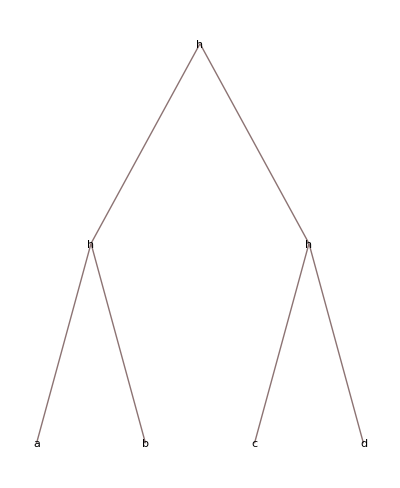

```mathematica
h[h[a,b],h[c,d]]//TreeForm
```

```mathematica
Map[g,h[h[a,b],h[c,d]],{2}]
```

h[h[g[a],g[b]],h[g[c],g[d]]]

```mathematica
Map[g,{{a,b},{c,d,e}},{2}]
```

{{g[a],g[b]},{g[c],g[d],g[e]}}

```mathematica
Map[g,{{a,b},{c,d,e}},2]
```

{g[{g[a],g[b]}],g[{g[c],g[d],g[e]}]}

##### Mapeando funciones del sistema

```mathematica
Map[Head,{2,π,22/7,2+ⅈ}]
```

{Integer,Symbol,Rational,Complex}

```mathematica
Reverse/@{{a,b},{c,d},{e,f}}
```

{{b,a},{d,c},{f,e}}

```mathematica
Sort[{{2,6,3,5},{4,1,3}}]
```

{{4,1,3},{2,6,3,5}}

```mathematica
Sort/@{{2,6,3,5},{4,1,3}}
```

{{2,3,5,6},{1,3,4}}

##### Mapeando funciones predefinidas

```mathematica
f[x_]:=x^2
```

```mathematica
f/@{5,π,γ}
```

{25,π^2,γ^2}

```mathematica
f[{5,π,γ}]
```

{25,π^2,γ^2}

```mathematica
f[x_]:={x,x}
```

```mathematica
f/@{5,π,γ}
```

{{5,5},{π,π},{γ,γ}}

```mathematica
f[{5,π,γ}]
```

{{5,π,γ},{5,π,γ}}

##### Mapeando funciones puras

```mathematica
Map[(#^3)&,{3,2,7}]
```

{27,8,343}

```mathematica
(#^3)&/@{3,2,7}
```

{27,8,343}

```mathematica
Map[(#^3)&,#]&[{3,2,7}]
```

{27,8,343}

```mathematica
Map[(#^3)&,#]&[{a,c,v,b}]
```

{a^3,c^3,v^3,b^3}

```mathematica
Function[y,Map[Function[x,x^3],y]][{3,2,7}]
```

{27,8,343}

#### MapAt

```mathematica
MapAt[g,{{a,b},{c,d,e}},{2,3}]
```

{{a,b},{c,d,g[e]}}

```mathematica
MapAt[g,{{a,b},{c,d,e}},{{2,3},{2},{1,1}}]
```

{{g[a],b},g[{c,d,g[e]}]}

#### MapIndexed

```mathematica
MapIndexed[f,{a,b,c,d}]
```

{f[a,{1}],f[b,{2}],f[c,{3}],f[d,{4}]}

```mathematica
MapIndexed[f,{{a,b},{c,d}},{2}]
```

{{f[a,{1,1}],f[b,{1,2}]},{f[c,{2,1}],f[d,{2,2}]}}

```mathematica
MapIndexed[f,{{a},{b},{c},{d}},{2}]
```

{{f[a,{1,1}]},{f[b,{2,1}]},{f[c,{3,1}]},{f[d,{4,1}]}}

```mathematica
Clear[f]
```

```mathematica
MapIndexed[If[#2[[1]]==#2[[2]],f[#1],#1]&,RandomInteger[{0,1},{5,5}],{2}]//MatrixForm
```

(f[1] | 0 | 1 | 0 | 1
0 | f[0] | 1 | 1 | 0
0 | 1 | f[1] | 1 | 0
1 | 0 | 0 | f[0] | 0
0 | 1 | 0 | 0 | f[1])

#### Ejemplo

Sumar el vector {a, b} a todos los elementos de una lista de vectores

```mathematica
{{1,1},{2,2},{3,3},{4,4}}+{a,b}
```

Thread::tdlen: Objects of unequal length in {{1,1},{2,2},{3,3},{4,4}}+{a,b} cannot be combined.

{a,b}+{{1,1},{2,2},{3,3},{4,4}}

```mathematica
{{1,1},{2,2},{3,3},{4,4}}+{{a,b}}
```

Thread::tdlen: Objects of unequal length in {{1,1},{2,2},{3,3},{4,4}}+{{a,b}} cannot be combined.

{{a,b}}+{{1,1},{2,2},{3,3},{4,4}}

```mathematica
#+{a,b}&/@{{1,1},{2,2},{3,3},{4,4}}
```

{{1+a,1+b},{2+a,2+b},{3+a,3+b},{4+a,4+b}}

## Manipulación de Expresiones

### Thread and MapThread

Thread[f[{a, b, c}]]      				{f[a], f[b], f[c]}
Thread[f[h[a, b, c]], h]				h[f[a], f[b], f[c]]
Thread[f[{a, b, c}, {A, B, C}]]      	{f[a, A], f[b, B], f[c, C]}

MapThread[f, {{a, b, c}, {x, y, z}}]	{f[a, x], f[b, y], f[c, z]}

#### Thread

```mathematica
Thread[f[{a,b,c}]]
```

{f[a],f[b],f[c]}

```mathematica
Thread[f[h[a,b,c]]]
```

f[h[a,b,c]]

```mathematica
Thread[f[h[a,b,c]],h]
```

h[f[a],f[b],f[c]]

```mathematica
Thread[f[{a,b,c},x]]
```

{f[a,x],f[b,x],f[c,x]}

```mathematica
Thread[f[{a,b,c},{x,y,z}]]
```

{f[a,x],f[b,y],f[c,z]}

```mathematica
Thread[f[{a,b,c},{w,x,y,z}]]
```

Thread::tdlen: Objects of unequal length in f[{a,b,c},{w,x,y,z}] cannot be combined.

f[{a,b,c},{w,x,y,z}]

```mathematica
Thread[f[h[a,b,c],h[x,y,z]],h]
```

h[f[a,x],f[b,y],f[c,z]]

#### MapThread

```mathematica
MapThread[f,{{a,b,c},{x,y,z}}]
```

{f[a,x],f[b,y],f[c,z]}

```mathematica
MapThread[f,{{{a,b},{c,d}},{{u,v},{s,t}}}]
```

{f[{a,b},{u,v}],f[{c,d},{s,t}]}

```mathematica
MapThread[f,{{{a,b},{c,d}},{{u,v},{s,t}}},2]
```

{{f[a,u],f[b,v]},{f[c,s],f[d,t]}}

```mathematica
MapThread[Power,{{2,6,3},{5,1,2}}]
```

{32,6,9}

```mathematica
MapThread[List,{{5,3,2},{6,4,9},{4,1,4}}]
```

{{5,6,4},{3,4,1},{2,9,4}}

```mathematica
Transpose[{{5,3,2},{6,4,9},{4,1,4}}]
```

{{5,6,4},{3,4,1},{2,9,4}}

#### Ejemplo:

Formando igualdades y reglas de dos listas

```mathematica
{a,b,c}=={x,y,z}//FullForm
```

Equal[List[a,b,c],List[x,y,z]]

```mathematica
Thread[{a,b,c}=={x,y,z}]
```

{a==x,b==y,c==z}

```mathematica
%//FullForm
```

List[Equal[a,x],Equal[b,y],Equal[c,z]]

```mathematica
vars={x1,x2,x3};
values={1,2,3};
```

```mathematica
vars->values//FullForm
```

Rule[List[x1,x2,x3],List[1,2,3]]

```mathematica
Thread[vars->values]
```

{x1→1,x2→2,x3→3}

```mathematica
%//FullForm
```

List[Rule[x1,1],Rule[x2,2],Rule[x3,3]]

## Manipulación de Expresiones

### Apply

Apply[f,{a,b,c}]  or  f @@ {a,b,c}   		Calculate f[a,b,c]
Apply[f, h[a,b,c]]  or  f @@ h[a,b,c]   	Calculate f[a,b,c]
Apply[f, expr, levels]   					Apply f to specified levels of expr

#### Ejemplos básicos

```mathematica
Apply[h,{a,b,c}]
```

h[a,b,c]

```mathematica
Apply[h,g[a,b,c]]
```

h[a,b,c]

```mathematica
h@@g[a,b,c]
```

h[a,b,c]

```mathematica
f@@{1,4,5,3}
```

f[1,4,5,3]

```mathematica
Plus@@{1,4,5,3}
```

13

```mathematica
Plus@@{{1,2,3},{5,6,7}}
```

{6,8,10}

```mathematica
Table@@{s[i],{i,2}}
```

{s[1],s[2]}

#### Apply a primer nivel

```mathematica
Plus@@#&/@{{1,2,3},{5,6,7}}
```

{6,18}

```mathematica
Apply[f,{{a,b},{c,d}},1]
```

{f[a,b],f[c,d]}

```mathematica
Apply[Plus,{{1,2,3},{5,6,7}},1]
```

{6,18}

```mathematica
Plus@@@{{1,2,3},{5,6,7}}
```

{6,18}

#### Ejemplo

Calculo de la media de una lista de números

```mathematica
mean[list_]:=(Plus@@list)/Length[list]
```

```mathematica
mean[{4,5,6}]
```

5

```mathematica
mean[Range[23]]
```

12

## Manipulación de Expresiones

### Inner and Outer

Inner[f,{a,b,c},{A,B,C}]        		f[a, A] + f[b, B] + f[c, C]
Inner[f,{a,b,c},{A,B,C},g]      		g[f[a, A], f[b, B], f[c, C]]

Outer[f,{a,b,c},{A,B,C}]        		{{f[a, A], f[a, B], f[a, C]}, 
                                 			  {f[b, A], f[b, B], f[b, C]}, 
                                 			  {f[c, A], f[c, B], f[c, C]}}

#### Inner

```mathematica
Inner[f,{a,b,c},{2,3,4},g]
```

g[f[a,2],f[b,3],f[c,4]]

```mathematica
Inner[Times,{a,b,c},{x,y,z},Plus]
```

a x+b y+c z

```mathematica
{a,b,c}.{x,y,z}
```

a x+b y+c z

```mathematica
Inner[List,{a,b,c},{x,y,z},Plus]
```

{a+b+c,x+y+z}

#### Outer

```mathematica
Outer[f,{a,b},{2,3,4}]
```

{{f[a,2],f[a,3],f[a,4]},{f[b,2],f[b,3],f[b,4]}}

```mathematica
Flatten[Outer[List,{a,b},{2,3,4}],1]
```

{{a,2},{a,3},{a,4},{b,2},{b,3},{b,4}}

## Funciones Iterativas

### Nest y NestList

Nest[f,x0,3]       		f[f[f[x0]]] 
NestList[f,x0,3]   		{x0, f[x0], f[f[x0]], f[f[f[x0]]]}

#### Ejemplos básicos

```mathematica
Nest[g,a,4]
```

g[g[g[g[a]]]]

```mathematica
NestList[g,a,4]
```

{a,g[a],g[g[a]],g[g[g[a]]],g[g[g[g[a]]]]}

```mathematica
cos = NestList[Cos,0.85,30]
```

{0.85,0.659983,0.790003,0.703843,0.76236,0.723208,0.749687,0.731902,0.743904,0.73583,0.741274,0.737609,0.740079,0.738416,0.739536,0.738781,0.73929,0.738947,0.739178,0.739023,0.739127,0.739057,0.739104,0.739072,0.739094,0.739079,0.739089,0.739082,0.739087,0.739084,0.739086}

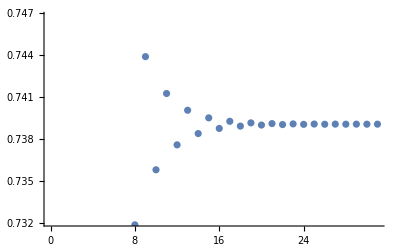

```mathematica
ListPlot[cos]
```

#### Ejemplo: Fracciones continuas

```mathematica
f[x_]:=1/(1+x)
```

```mathematica
Nest[f,x,7]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x)))))))

```mathematica
NestList[f,x,7]
```

{x,1/(1+x),1/(1+1/(1+x)),1/(1+1/(1+1/(1+x))),1/(1+1/(1+1/(1+1/(1+x)))),1/(1+1/(1+1/(1+1/(1+1/(1+x))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x)))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x)))))))}

```mathematica
%//Simplify
```

{x,1/(1+x),(1+x)/(2+x),(2+x)/(3+2 x),(3+2 x)/(5+3 x),(5+3 x)/(8+5 x),(8+5 x)/(13+8 x),(13+8 x)/(21+13 x)}

```mathematica
Plus@@%
```

x+1/(1+x)+(1+x)/(2+x)+(2+x)/(3+2 x)+(3+2 x)/(5+3 x)+(5+3 x)/(8+5 x)+(8+5 x)/(13+8 x)+(13+8 x)/(21+13 x)

```mathematica
%//Together
```

(303102+1413116 x+2868985 x^2+3308641 x^3+2366294 x^4+1071973 x^5+299313 x^6+46844 x^7+3120 x^8)/((1+x) (2+x) (3+2 x) (5+3 x) (8+5 x) (13+8 x) (21+13 x))

#### Ejemplo: Algoritmo de Newton (x_i→x_i-(f(x_i))/(f'(x_i)))

```mathematica
√2//N
```

1.41421

```mathematica
f[x_]:=x^2-2
```

```mathematica
Nest[(#-f[#]/f'[#])&,1.,20]
```

1.41421

```mathematica
findRootWithNest[f_,xo_,steps_]:=With[{fp=f'},Nest[(#-f[#]/fp[#])&,N[xo],steps]]
```

```mathematica
findRootWithNest[(#^2-2)&,1,20]
```

1.41421

```mathematica
findRootWithNest[(Cos[#]-x)&,1,20]
```

1.5708

## Funciones Iterativas

### NestWhile y NestWhileList

NestWhile[f,x0,test]       		f[…f[f[x0]]…] until result no longer yields true 
NestWhileList[f,x0,test]   		{x0, f[x0], f[f[x0]], …} until result no longer
									yields true

#### Ejemplo

```mathematica
Log[Log[Log[Log[100]]]]//Positive
```

False

```mathematica
NestWhile[Log,100,Positive]
```

Log[Log[Log[Log[100]]]]

```mathematica
NestWhileList[Log,100,Positive]
```

{100,Log[100],Log[Log[100]],Log[Log[Log[100]]],Log[Log[Log[Log[100]]]]}

```mathematica
NestWhileList[Log,100.,Positive]
```

{100.,4.60517,1.52718,0.423423,-0.859384}

#### Ejemplo

```mathematica
f[x_]:=x/2
```

```mathematica
NestWhile[f,123456,EvenQ]
```

1929

```mathematica
NestWhileList[f,123456,EvenQ]
```

{123456,61728,30864,15432,7716,3858,1929}

#### Ejemplo

Encontrar el siguiente número primo después de 53627674382

```mathematica
NestWhile[#+1&,53627674382,!PrimeQ[#]&]
```

53627674409

```mathematica
nextPrime[n_]:=NestWhile[#+1&,n,!PrimeQ[#]&]
```

```mathematica
nextPrime[53627674382]
```

53627674409

#### Ejemplo

Algoritmo de Newton

```mathematica
findRootWithNestWhile[f_,xo_,ϵ_:10^-10,max_:100]:=
With[{fp=f'},
NestWhile[(#-f[#]/fp[#])&,N[xo],(Abs[f[#]]>ϵ)&,1,max]
]
```

```mathematica
findRootWithNestWhile[(Cos[#]-#)&,1]
```

0.739085

```mathematica
findRootWithNestWhile[(Cos[#]-#)&,1,10^-2]
```

0.739113

```mathematica
findRootWithNestWhile[(#^2-50)&,1,10^-16]
```

7.07107

```mathematica
findRootWithNestWhile[(Cos[#]-#)&,1,10^-16]
```

0.739085

## Funciones Iterativas

### Fold y FoldList

Fold[f, x0, {a,b,c}]      		f[f[f[x0,a],b],c] 
FoldList[f, x0, {a,b,c}]  		{x0, f[x0,a], f[f[x0,a],b],f[f[f[x0,a],b],c]}

#### Ejemplos básicos

```mathematica
Fold[f,x,{a,b,c,d}]
```

```mathematica
FoldList[f,x,{a,b,c,d}]
```

#### Ejemplo: Sumas acumuladas

```mathematica
FoldList[Plus,0,{a,b,c,d}]
```

```mathematica
Accumulate[{a,b,c,d}]
```

```mathematica
FoldList[Plus,0,{3,5,2,4}]
```

#### Ejemplo : el factorial

```mathematica
fact[n_]:=FoldList[Times,1,Range[n]]
```

```mathematica
fact[10]
```

#### Ejemplo: caminante aleatorio en 1D

```mathematica
decisiones=Table[2 Random[Integer]-1,{10}]
```

```mathematica
decisiones=2RandomInteger[{0,1},{10}]-1
```

```mathematica
posiciones=FoldList[Plus,0,decisiones]
```

#### Ejemplo: caminante aleatorio en 2D

```mathematica
pasos={{0,1},{1,0},{-1,0},{0,-1}}
```

{{0,1},{1,0},{-1,0},{0,-1}}

```mathematica
decisiones=RandomChoice[pasos,10]
```

{{0,1},{-1,0},{-1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{0,-1},{-1,0}}

```mathematica
posiciones=FoldList[Plus,0,decisiones]
```

{0,{0,1},{-1,1},{-2,1},{-1,1},{-1,2},{-1,3},{0,3},{1,3},{1,2},{0,2}}

```mathematica
randomWalk2D[pasos_]:=FoldList[Plus,{0,0},RandomChoice[{{0,1},{1,0},{-1,0},{0,-1}},pasos]]
```

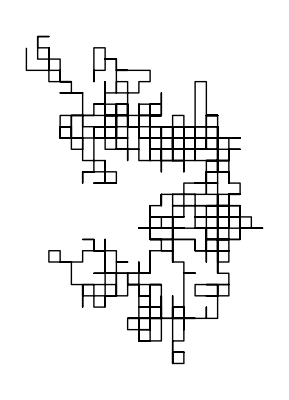

```mathematica
Graphics[Line[randomWalk2D[1000]]]
```

## Funciones Iterativas

### FixedPoint y FixedPointList

FixedPoint[f,x0]         		Apply f repeatedly until convergence
FixedPointList[f,x0]     		Store the iterations in a list
FixedPoint[f,x0,n]       		Apply f at most n times
FixedPointList[f,x0,n]   		Store the iterations in a list

#### Ejemplo básico

```mathematica
f[x_]:=1+Floor[x/2]
```

```mathematica
NestList[f,1000,20]
```

{1000,501,251,126,64,33,17,9,5,3,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
FixedPoint[f,1000]
```

2

```mathematica
FixedPoint[f,1000,7]
```

9

#### Ejemplo: Punto fijo de x=cos x

```mathematica
FindRoot[x==Cos[x],{x,1}]
```

{x→0.739085}

```mathematica
FixedPoint[Cos,1,3]
```

Cos[Cos[Cos[1]]]

```mathematica
FixedPoint[Cos,1.]
```

0.739085

```mathematica
FixedPointList[Cos,1.] // InputForm
```

{1., 0.5403023058681398, 
 0.8575532158463934, 
 0.6542897904977791, 
 0.7934803587425656, 
 0.7013687736227565, 
 0.7639596829006542, 
 0.7221024250267077, 
 0.7504177617637605, 
 0.7314040424225098, 
 0.7442373549005569, 
 0.7356047404363474, 
 0.7414250866101092, 
 0.7375068905132428, 
 0.7401473355678757, 
 0.7383692041223232, 
 0.7395672022122561, 
 0.7387603198742113, 
 0.7393038923969059, 
 0.7389377567153445, 
 0.7391843997714936, 
 0.7390182624274122, 
 0.7391301765296711, 
 0.7390547907469174, 
 0.7391055719265363, 
 0.7390713652989449, 
 0.7390944073790913, 
 0.739078885994992, 
 0.7390893414033927, 
 0.7390822985224024, 
 0.7390870426953322, 
 0.7390838469650002, 
 0.7390859996481299, 
 0.7390845495752126, 
 0.7390855263619245, 
 0.7390848683867142, 
 0.7390853116067619, 
 0.7390850130484203, 
 0.7390852141609171, 
 0.739085078689123, 
 0.7390851699445544, 
 0.7390851084737987, 
 0.7390851498812394, 
 0.7390851219886894, 
 0.7390851407774467, 
 0.7390851281211138, 
 0.7390851366465718, 
 0.7390851309037207, 
 0.7390851347721744, 
 0.7390851321663374, 
 0.7390851339216605, 
 0.7390851327392538, 
 0.7390851335357372, 
 0.7390851329992164, 
 0.7390851333606233, 
 0.7390851331171753, 
 0.7390851332811648, 
 0.7390851331706995, 
 0.7390851332451103, 
 0.7390851331949863, 
 0.7390851332287504, 
 0.7390851332060064, 
 0.7390851332213271, 
 0.7390851332110069, 
 0.7390851332179587, 
 0.7390851332132758, 
 0.7390851332164302, 
 0.7390851332143055, 
 0.7390851332157367, 
 0.7390851332147726, 
 0.739085133215422, 
 0.7390851332149846, 
 0.7390851332152792, 
 0.7390851332150807, 
 0.7390851332152145, 
 0.7390851332151244, 
 0.7390851332151851, 
 0.7390851332151441, 
 0.7390851332151718, 
 0.7390851332151531, 
 0.7390851332151657, 
 0.7390851332151572, 
 0.7390851332151629, 
 0.7390851332151591, 
 0.7390851332151617, 
 0.7390851332151599, 
 0.7390851332151611, 
 0.7390851332151603, 
 0.7390851332151609, 
 0.7390851332151605, 
 0.7390851332151608, 
 0.7390851332151606, 
 0.7390851332151607}

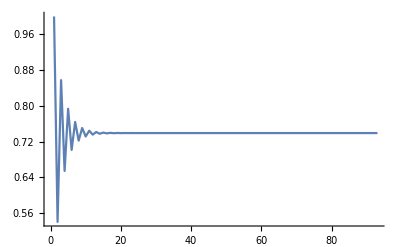

```mathematica
ListLinePlot[%,PlotRange->All]
```

## Funciones como Programas

### Composición de Funciones

Composition[f,g][x] 							f[g[x]]
RightComposition[f,g][x,y]						g[f[x]]
ComposeList[{f,g},x]							{x,f[x], g[f[x]]}

#### Ejemplos

```mathematica
{t[h[g[x]]],x//g//h//t,t@h@g@x}
```

{t[h[g[x]]],t[h[g[x]]],t[h[g[x]]]}

```mathematica
{Composition[t,h,g][x],RightComposition[t,h,g][x]}
```

{t[h[g[x]]],g[h[t[x]]]}

```mathematica
{t@*h@*g@x,t/*h/*g@x}
```

{t[h[g[x]]],g[h[t[x]]]}

#### Seguimiento de programas

```mathematica
Sin[Cos[Tan[4.0]]]
```

0.390649

```mathematica
Trace[Sin[Cos[Tan[4.0]]]]
```

{{{Tan[4.],1.15782},Cos[1.15782],0.401336},Sin[0.401336],0.390649}

```mathematica
Trace[Sin[Cos[Tan[4.0]]],Cos]
```

{{Cos[1.15782],0.401336}}

## Funciones como Programas

### Construyendo Programas

#### Problema:

Determinar si todos los elementos de una lista son pares

```mathematica
EvenQ[2]
```

True

```mathematica
Map[EvenQ,{2,4,6,7,8}]
```

{True,True,True,False,True}

```mathematica
Apply[And,%]
```

False

```mathematica
Apply[And,Map[EvenQ,{2,4,6,7,8}]]
```

False

```mathematica
setEvenQ[lista_]:=Apply[And,Map[EvenQ,lista]]
```

```mathematica
RandomInteger[{1,10},10]
```

```mathematica
setEvenQ[%]
```

#### Problema:

Devolver los elementos de una lista de números positivos que son mayores que todos los números precedentes en la lista

```mathematica
FoldList[Max,0,{3,1,6,5,4,8,7}]
```

{0,3,3,6,6,6,8,8}

```mathematica
Rest[%]
```

{3,3,6,6,6,8,8}

```mathematica
Union[%]
```

{3,6,8}

```mathematica
Union[Rest[FoldList[Max,0,{3,1,6,5,4,8,7}]]]
```

{3,6,8}

```mathematica
maxima[lista_]:=Union[Rest[FoldList[Max,0,lista]]]
```

```mathematica
RandomInteger[{1,10},10]
```

{2,8,6,4,10,10,4,7,4,10}

```mathematica
maxima[%]
```

{2,8,10}

#### Problema:

Creación de un juego de cartas.

```mathematica
{♣,♢,♡,♠}
```

{♣,♢,♡,♠}

```mathematica
Join[Range[2,10],{𝒥,𝒬,𝒦,𝒜}]
```

{2,3,4,5,6,7,8,9,10,𝒥,𝒬,𝒦,𝒜}

```mathematica
Outer[List,%%,%]
```

{{{♣,2},{♣,3},{♣,4},{♣,5},{♣,6},{♣,7},{♣,8},{♣,9},{♣,10},{♣,𝒥},{♣,𝒬},{♣,𝒦},{♣,𝒜}},{{♢,2},{♢,3},{♢,4},{♢,5},{♢,6},{♢,7},{♢,8},{♢,9},{♢,10},{♢,𝒥},{♢,𝒬},{♢,𝒦},{♢,𝒜}},{{♡,2},{♡,3},{♡,4},{♡,5},{♡,6},{♡,7},{♡,8},{♡,9},{♡,10},{♡,𝒥},{♡,𝒬},{♡,𝒦},{♡,𝒜}},{{♠,2},{♠,3},{♠,4},{♠,5},{♠,6},{♠,7},{♠,8},{♠,9},{♠,10},{♠,𝒥},{♠,𝒬},{♠,𝒦},{♠,𝒜}}}

```mathematica
Flatten[%,1]
```

{{♣,2},{♣,3},{♣,4},{♣,5},{♣,6},{♣,7},{♣,8},{♣,9},{♣,10},{♣,𝒥},{♣,𝒬},{♣,𝒦},{♣,𝒜},{♢,2},{♢,3},{♢,4},{♢,5},{♢,6},{♢,7},{♢,8},{♢,9},{♢,10},{♢,𝒥},{♢,𝒬},{♢,𝒦},{♢,𝒜},{♡,2},{♡,3},{♡,4},{♡,5},{♡,6},{♡,7},{♡,8},{♡,9},{♡,10},{♡,𝒥},{♡,𝒬},{♡,𝒦},{♡,𝒜},{♠,2},{♠,3},{♠,4},{♠,5},{♠,6},{♠,7},{♠,8},{♠,9},{♠,10},{♠,𝒥},{♠,𝒬},{♠,𝒦},{♠,𝒜}}

```mathematica
cardDeck=Flatten[Outer[List,{♣,♢,♡,♠},Join[Range[2,10],{𝒥,𝒬,𝒦,𝒜}]],1]
```

{{♣,2},{♣,3},{♣,4},{♣,5},{♣,6},{♣,7},{♣,8},{♣,9},{♣,10},{♣,𝒥},{♣,𝒬},{♣,𝒦},{♣,𝒜},{♢,2},{♢,3},{♢,4},{♢,5},{♢,6},{♢,7},{♢,8},{♢,9},{♢,10},{♢,𝒥},{♢,𝒬},{♢,𝒦},{♢,𝒜},{♡,2},{♡,3},{♡,4},{♡,5},{♡,6},{♡,7},{♡,8},{♡,9},{♡,10},{♡,𝒥},{♡,𝒬},{♡,𝒦},{♡,𝒜},{♠,2},{♠,3},{♠,4},{♠,5},{♠,6},{♠,7},{♠,8},{♠,9},{♠,10},{♠,𝒥},{♠,𝒬},{♠,𝒦},{♠,𝒜}}

#### Problema

Barajar de manera perfecta un juego de cartas.

```mathematica
list=Range[6]
```

{1,2,3,4,5,6}

```mathematica
Partition[list,Length[list]/2]
```

{{1,2,3},{4,5,6}}

```mathematica
Transpose[%]
```

{{1,4},{2,5},{3,6}}

```mathematica
Flatten[%,1]
```

{1,4,2,5,3,6}

```mathematica
Flatten[Transpose[Partition[list,Length[list]/2]],1]
```

{1,4,2,5,3,6}

```mathematica
shuffle[list_]:=Flatten[Transpose[Partition[list,Length[list]/2]],1]
```

```mathematica
shuffle[cardDeck]
```

{{♣,2},{♡,2},{♣,3},{♡,3},{♣,4},{♡,4},{♣,5},{♡,5},{♣,6},{♡,6},{♣,7},{♡,7},{♣,8},{♡,8},{♣,9},{♡,9},{♣,10},{♡,10},{♣,𝒥},{♡,𝒥},{♣,𝒬},{♡,𝒬},{♣,𝒦},{♡,𝒦},{♣,𝒜},{♡,𝒜},{♢,2},{♠,2},{♢,3},{♠,3},{♢,4},{♠,4},{♢,5},{♠,5},{♢,6},{♠,6},{♢,7},{♠,7},{♢,8},{♠,8},{♢,9},{♠,9},{♢,10},{♠,10},{♢,𝒥},{♠,𝒥},{♢,𝒬},{♠,𝒬},{♢,𝒦},{♠,𝒦},{♢,𝒜},{♠,𝒜}}

#### Problema

Extraer aleatoriamente cierto número de cartas de una baraja

```mathematica
lista={a,b,c,d,e}
```

```mathematica
RandomInteger[{1,Length[lista]}]
```

```mathematica
Delete[lista,RandomInteger[{1,Length[lista]}]]
```

```mathematica
removeRand[lis_]:=Delete[lis,RandomInteger[{1,Length[lis]}]]
```

```mathematica
removeRand[lista]
```

```mathematica
Nest[removeRand,cardDeck,5]
```

```mathematica
Complement[cardDeck,%]
```

```mathematica
deal[n_]:=Complement[cardDeck,Nest[removeRand,cardDeck,n]]
```

```mathematica
deal[5]
```

```mathematica
deal[10]
```

## Funciones como Programas

### One–Liners

#### Problema:

Unsorted Union

```mathematica
unsortedUnion[lista_]:=Gather[Flatten[lista,1]][[All,1]]
```

```mathematica
Partition[RandomInteger[{1,10},12],3]
```

```mathematica
unsortedUnion[%]
```

#### Problema

Calcular el total en soles juntando todas las moneditas que tienes en el bolsillo.

```mathematica
pocketChange[lista_,coins_, values_]:=(Count[lista,#1]&/@coins).values
```

```mathematica
coins={d,v,c,s,s2,s5}
```

```mathematica
values={0.1,0.2,0.5,1,2,5}
```

```mathematica
sampleCoins=coins[[RandomInteger[{1,6},{40}]]]
```

```mathematica
pocketChange[sampleCoins,coins,values]
```

#### Problema

Calcular la distancia de Hamming definida como el número de elementos diferentes de dos listas.

```mathematica
hammingDistance1[lista1_,lista2_]:=Count[MapThread[ SameQ,{lista1,lista2}],False]
```

```mathematica
hammingDistance1[{1,0,0,1,1},{0,1,0,1,0}]
```

```mathematica
hammingDistance2[lista1_,lista2_]:=Plus@@BitXor@@@Transpose[{lista1,lista2}]
```

```mathematica
hammingDistance2[{1,0,0,1,1},{0,1,0,1,0}]
```

```mathematica
data1=Table[RandomInteger[],{10^6}];
data2=Table[RandomInteger[],{10^6}];
```

```mathematica
Timing[hammingDistance1[data1,data2]]
```

```mathematica
Timing[hammingDistance2[data1,data2]]
```

```mathematica
Timing[HammingDistance[data1,data2]]
```

#### El problema de Josephus

n personas están alineadas haciendo una cola. La primera persona se mueve al final de la cola, la segunda persona es eliminada, la tercera persona se mueve al final de la cola, y asi sucesivamente hasta que sólo una persona queda. ¿Qué posición ocupa esta persona en la lista inicial?

```mathematica
survivor[lista_]:=Nest[Rest[RotateLeft[#1]]&,lista,Length[lista]-1]
```

```mathematica
survivor[Range[35]]
```

```mathematica
survivors=Flatten[survivor[#]&/@Table[Range[n],{n,50}]]
```

```mathematica
ListPlot[survivors]
```

#### Borrar ocurrencias consecutivas

Borrar ocurrencias consecutivas de un mismo elemento en una lista

```mathematica
removeRepetitions[lis_]:=Fold[If[#2==Last[#1],#1,Append[#1,#2]]&,{First[lis]},Rest[lis]]
```

```mathematica
removeRepetitions[{0,1,1,2,2,2,1,1}]
```

```mathematica
removeRepetitions2[lis_]:=Split[lis][[All,1]]
```

```mathematica
removeRepetitions2[{0,1,1,2,2,2,1,1}]
```

```mathematica
table=RandomInteger[{0,5},{10^5}];
```

```mathematica
removeRepetitions[table];//AbsoluteTiming
removeRepetitions2[table];//AbsoluteTiming
```

## Funciones como Programas

### Diseño de programas

#### Usando funciones auxiliares no localizadas

```mathematica
Clear[cardDeck,removeRand,deal]
```

```mathematica
cardDeck=Flatten[Outer[List,{♣,♢,♡,♠},Join[Range[2,10],{𝒥,𝒬,𝒦,𝒜}]],1]
```

```mathematica
removeRand[lis_]:=Delete[lis,Random[Integer,{1,Length[lis]}]]
```

```mathematica
deal[n_]:=Complement[cardDeck,Nest[removeRand,cardDeck,n]]
```

```mathematica
deal[5]
```

#### Usando funciones auxiliares localizadas

```mathematica
Clear[cardDeck,removeRand,deal]
```

```mathematica
deal[n_]:=Module[
{cardDeck,removeRand},

cardDeck=Flatten[Outer[List,{♣,♢,♡,♠},
Join[Range[2,10],{𝒥,𝒬,𝒦,𝒜}]],1];

removeRand[lis_]:=Delete[lis,
Random[Integer,{1,Length[lis]}]];

Complement[cardDeck,Nest[removeRand,cardDeck,n]]
]
```

```mathematica
deal[5]
```

#### Usando funciones puras

```mathematica
Clear[deal]
deal[n_]:=Module[
{cardDeck},

cardDeck=Flatten[Outer[List,{♣,♢,♡,♠},
Join[Range[2,10],{𝒥,𝒬,𝒦,𝒜}]],1];

Complement[cardDeck,
Nest[Delete[#,Random[Integer,{1,Length[#]}]]&,
cardDeck,n]]
]
```

#### Separando funciones utilitarias

```mathematica
deal[5]
```

```mathematica
chooseWithoutReplacement[lis_,n_]:=Complement[lis,
Nest[(Delete[#,Random[Integer,{1,Length[#]}]])&,lis,n]]
```

```mathematica
chooseWithoutReplacement[{m,s,d,e,p,f,j},3]
```

```mathematica
Clear[deal]
deal[n_]:=Module[{cardDeck},

cardDeck=Flatten[Outer[List,{♣,♢,♡,♠},
Join[Range[2,10],{𝒥,𝒬,𝒦,𝒜}]],1];

chooseWithoutReplacement[cardDeck,n]
]
```

```mathematica
deal[5]
```